# Parity Solutions (version 31-07-2021)

## Sequencing elementary rules 254, 76, 132, 222, 184 and 252 [Lee, Xu and Chau, 2001]

### Reference

The original reference and its simplified version:

K.M. Lee, H. Xu and H.F. Chau. "Parity problem with a cellular automaton solution". Physical Review E, 64 : 026702/1 - 026702/4, 2001.

C.L.M. Martins and P.P.B. de Oliveira. “Improvement of a result on sequencing elementary cellular automata rules for solving the parity problem”. Electronic Notes in Theoretical Computer Science, 252:103-119, 2009.

```mathematica
-Graphics-
-Graphics-
-Graphics-
```

### Functions

```mathematica
LXCca[sigma_List,printout_:Off]:=
Module[{N=Length[sigma]},
Flatten[Reap[Sow[{sigma}];
If[N>0,
If[printout==On,If[EvenQ[Count[sigma,1]],Print["Even parity."],Print["Odd parity."]]];
If[OddQ[N],Sigma1[sigma],
If[OddQ[N/2],opS[Sigma1[sigma]], opS[Sigma2[sigma]]]]]]⟦-1,-1⟧,1]];
```

```mathematica
Sigma1[binlist_List]:=
Module[{N=Length[binlist]},
Nest[Last[Sow[Rest[CellularAutomaton[{132,2,1}, Last[Sow[Rest[CellularAutomaton[{222,2,1}, #,⌊N/2⌋]]]],⌊N/2⌋]]]]&,binlist,⌊N/2⌋]];
```

```mathematica
Sigma2[binlist_List]:= Module[{N=Length[binlist]},Nest[opT[#]&,Sigma1[binlist],m[N]-1]];
```

```mathematica
m[N_]:=NestWhile[(#+1)&,1,EvenQ[N/2^#]&];
```

```mathematica
opS[binlist_List]:=
Module[{N=Length[binlist]},Last[Sow[Rest[CellularAutomaton[{254,2,1}, Last[Sow[CellularAutomaton[{76,2,1}, binlist,1,-1]]],⌈N/2⌉]]]]];
```

```mathematica
opT[binlist_List]:=
Module[{N=Length[binlist]},
Last[Sow[Rest[CellularAutomaton[{132,2,1}, Last[Sow[Rest[CellularAutomaton[{222,2,1}, 
Last[Sow[CellularAutomaton[{184,2,1}, Last[Sow[CellularAutomaton[{252,2,1},binlist,1,-1]]],1,-1]]],⌊N/2⌋]]]],⌊N/2⌋]]]]];
```

### Testing

```mathematica
TestLXC[ntimes_]:=
Module[{bitsin,bitsout,len},
Count[Table[(bitsout=Last[LXCca[bitsin=Table[Random[Integer],{len=Random[Integer,{1,150}]}]]];
If[(EvenQ[Count[bitsin,1]] ∧ Total[bitsout]===0) ∨ (OddQ[Count[bitsin,1]] ∧ Total[bitsout]===len),OK]),{ntimes}],OK]];
```

```mathematica
TestLXC[1000]
```

1000

```mathematica
Last@LXCca[Table[Random[Integer],{120}],On]
```

Odd parity.

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

### Visualisation (Estranho: funciona também para tamanhos pares...)

```mathematica
ArrayPlot[LXCca[Table[Random[Integer],{12}],On] ]
```

Even parity.

-Graphics-

```mathematica
{ArrayPlot[LXCca[{1,1,1,1,1,1,1,1,1,1},On] ],ArrayPlot[LXCca[{1,1,1,1,1,1,1,1,1,1,1},On] ]}
```

Even parity.

Odd parity.

{-Graphics-,-Graphics-}

```mathematica
ArrayPlot[LXCca[{1,0,1,0,0,1,1,0,1,0},On] ]
```

Odd parity.

-Graphics-

Even parity.

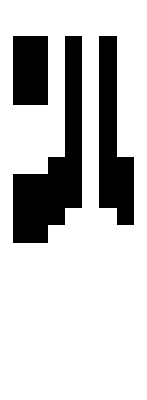

```mathematica
ArrayPlot[LXCca[Table[Random[Integer],{7}],On] ]
```

## The BFOm parity rule (radius 4) : perfect rule for odd - size

```mathematica
BFO=12766019579927887748851022493766362852538653477089610507586617786038145006190995664733646843131214325976648032120921367273971918968599273892908870567657472;
```

```mathematica
BFOm=12766019579927887748828308783632125137208948629571434199404394002667717405977989433935674396392364628033397327077046394244352827899915766421679960036933632;
```

```mathematica
Module[{icaux=RandomInteger[{0,1},101]},
Print[If[OddQ[Count[icaux,1]],"Odd ","Even "],"parity"];
ArrayPlot[CellularAutomaton[{BFOm,2,4},icaux,120],Mesh->False]]
```

Even parity

-Graphics-

```mathematica
(* BFOm is in a class with 4 equivalent rules *)
```

```mathematica
EquivalenceClass[BFOm,2,4]
```

{12766019579927887748828308783632125137208948629571434199404394002667717405977989433935674396392364628033397327077046394244352827899915766421679960036933632,13407604092447413382334775607167903323181879061119834494094272181747942880804482194482226030615956543831716842665154575092317103273751797700350095392703024,13381416670630950875030341748640845062758338580068811950958771282456257262157725325551590631775149365470041403629673084346673956612444528095105814755263376,12896351788858219667684585144530123604331821953299659568186791467002418602307806016770106156688043091070846873348655302908937012165529110743681756806709504}

```mathematica
(* BFOm doesn't have maximal symmetry pattern of any kind. *)
```

```mathematica
CountSymmetry[BFOm,2,4,{stBWTransform,stLRTransform,stBWLRTransform}]
```

{332,350,348}

```mathematica
Tally@MapThread[If[#1===#2,True,Style[#1,Blue]]&,RuleTable[#,2,4]&/@{BFO,BFOm}]//Column
```

{True,500}
{{{1,1,0,1,1,1,0,1,1},1},1}
{{{1,0,1,1,1,0,1,1,0},1},1}
{{{1,0,0,1,1,1,0,1,1},1},1}
{{{1,0,0,1,0,0,0,1,1},1},1}
{{{0,1,1,1,0,1,1,1,1},1},1}
{{{0,1,1,1,0,1,1,1,0},1},1}
{{{0,1,0,1,1,1,0,1,1},1},1}
{{{0,0,1,1,1,0,1,1,0},1},1}
{{{0,0,1,0,0,0,1,1,1},1},1}
{{{0,0,1,0,0,0,1,1,0},1},1}
{{{0,0,0,1,1,1,0,1,1},1},1}
{{{0,0,0,1,0,0,0,1,1},1},1}

## ECA rule 150 under asynchronous solution

```mathematica
Module[{icaux=RandomInteger[{0,1},411],tsteps},
tsteps=⌈1.1 Length[icaux]⌉;
Print[If[OddQ[Count[icaux,1]],"Odd ","Even "],"parity"];
ArrayPlot[AsynchronousCA[{150,2,1},icaux,tsteps,{Range[2,Length@icaux,2],Range[1,Length@icaux,2]}],Mesh->False]]
```

Even parity

-Graphics-

```mathematica
Module[{ecaRnum=150,icaux=RandomInteger[{0,1},411],tsteps},
tsteps=⌈1.1 Length[icaux]⌉;
Print[If[OddQ[Count[icaux,1]],"Odd ","Even "],"parity"];
{ArrayPlot[CellularAutomaton[ecaRnum,icaux,tsteps]],ArrayPlot[AsynchronousCA[{ecaRnum,2,1},icaux,tsteps,{Range[2,Length@icaux,2],Range[1,Length@icaux,2]}]]}]
```

Odd parity

{-Graphics-,-Graphics-}

### Details: even parity configurations of size L ( L = 4 l + 1 or L = 4 l + 3)

Even parity

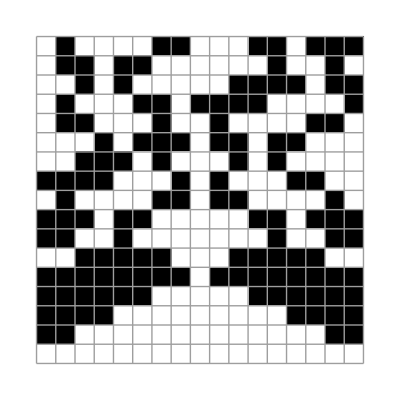

```mathematica
Module[{icaux={0,1,0,0,0,0,1,1,0,0,0,1,1,0,1,1,1},tsteps},
tsteps=Length[icaux]-1;
Print[If[OddQ[Count[icaux,1]],"Odd ","Even "],"parity"];
ArrayPlot[AsynchronousCA[{150,2,1},icaux,tsteps,{Range[2,Length@icaux,2],Range[1,Length@icaux,2]}],Mesh->True]]
```

### Details: odd parity configurations of size L ( L = 4 l + 1 or L = 4 l + 3)

```mathematica
Module[{icaux={0,1,0,1,0,0,1,1,1,0,0,1,1,1,0,1,0,1,1},tsteps},
tsteps=Length[icaux]-1;
Print[If[OddQ[Count[icaux,1]],"Odd ","Even "],"parity"];
ArrayPlot[AsynchronousCA[{150,2,1},icaux,tsteps,{Range[2,Length@icaux,2],Range[1,Length@icaux,2]}],Mesh->True]]
```

Odd parity

-Graphics-

## Solution with ECA rule 150 with asynchronous update schedule can be seen as a non-homogeneous CA with local parity rules and synchronous update

(cells are numbered from 1 to n, with n odd; and f denotes local parity rule on 3 inputs)
*for cell 1 : f_ 1 = f (x_n, x_ 1, f (x_ 1, x_ 2, x_ 3))
this is local parity on x_n, x_ 2, x_ 3
*for cells i in {2, 4, ..., n - 1} : f_i = f (x_ {i - 1}, x_i, x_ {i + 1})
this is local parity of radius 1
*for cells i in {3, 5, ..., n - 2} : f_i = f (f_ (x_ {i - 2}, x_ {i - 1}, x_i), x_i, f (x_i, x_ {i + 1}, x_ {i + 2}))
this is local parity of radius 2
*for cell n : f_n = f (f (x_ {n - 2}, x_ {n - 1}, x_n), x_n, x_ 1)
this is local parity on x_ {n - 2}, x_ {n - 1}, x_ 1

```mathematica
ParityHybridCA[N_Integer]:=
ArrayPlot[
Module[{randIC},
randIC=RandomInteger[{0,1},N];
Print[If[EvenQ[Total[randIC]],"Even", "Odd"]];
CASpatialComposition[
{{150,2,{{-1},{1},{2}}},
Sequence@@Riffle[
Table[{150,2,1},Length[Range[2,N-1,2]]],
Table[{ParityRule[2],2,2},Length[Range[3,N-2,2]]]],
{150,2,{{-2},{-1},{1}}}},
randIC,
⌈1.1 N⌉]]];
```

```mathematica
ParityHybridCA[411]
```

Even

-Graphics-

```mathematica
ParityHybridCAGraph[N_Integer]:=
Module[{edges,edge1,edgeN,evenEdges,oddEdges},
edge1={N->1,2->1,3->1};
edgeN={1->N,N-1->N,N-2->N};
evenEdges=Flatten[({#->#,#-1->#,#+1->#}&/@Range[2,N-1,2])];
oddEdges=Flatten[({#->#,#-2->#,#-1->#,#+1->#,#+2->#}&/@Range[3,N-2,2])];
edges=Join[edge1,edgeN,evenEdges,oddEdges];
Graph[edges,VertexLabels->"Name",PlotLabel->Row[{Style["N",Italic,Blue,FontSize->16],Style[" = "<>ToString[N],Blue,FontSize->16]}]]
];
```

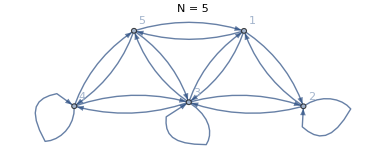
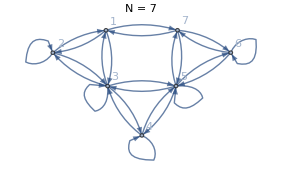
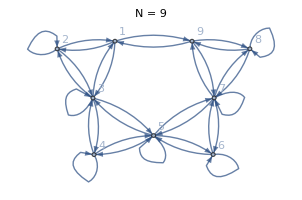
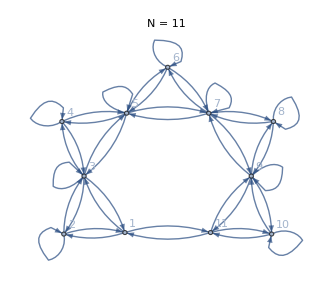
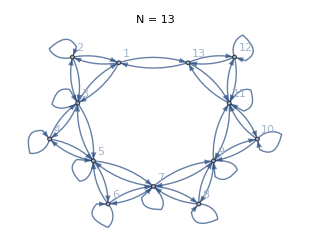
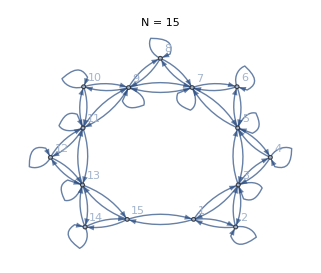

```mathematica
ParityHybridCAGraph[#]&/@Range[5,15,2]
```

```mathematica
(* Number of nodes with local parity rule with r=2 *)
FindSequenceFunction@{{5,1},{7,2},{9,3},{11,4},{13,5},{15,6}}
```

1/2 (-3+#1)&

```mathematica
(* Number of nodes with local parity rule with r=1 *)
Expand[L-(L-3)/2]
```

3/2+L/2

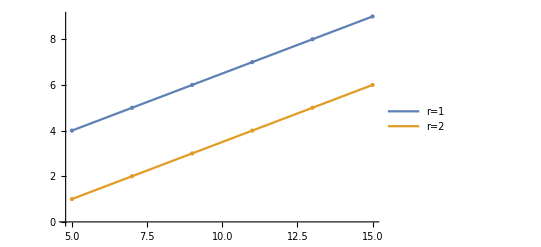

```mathematica
ListPlot[{{{5,4},{7,5},{9,6},{11,7},{13,8},{15,9}},{{5,1},{7,2},{9,3},{11,4},{13,5},{15,6}}},Joined->True,Mesh->All,PlotLegends->{"r=1","r=2"},PlotStyle->PointSize[Large]]
```

```mathematica
ParityHybridCAGraph[N_Integer]:=
Module[{edges,edge1,edgeN,evenEdges,oddEdges},
edge1={N->1,2->1,3->1};
edgeN={1->N,N-1->N,N-2->N};
evenEdges=Flatten[({#->#,#-1->#,#+1->#}&/@Range[2,N-1,2])];
oddEdges=Flatten[({#->#,#-2->#,#-1->#,#+1->#,#+2->#}&/@Range[3,N-2,2])];
edges=Join[edge1,edgeN,evenEdges,oddEdges];
Graph[edges,EdgeStyle->Black,VertexLabels->"Name",PlotLabel->Row[{Style["L",Italic,Black, FontSize->16],Style[" = "<>ToString[N],FontSize->16]}]]
];
```

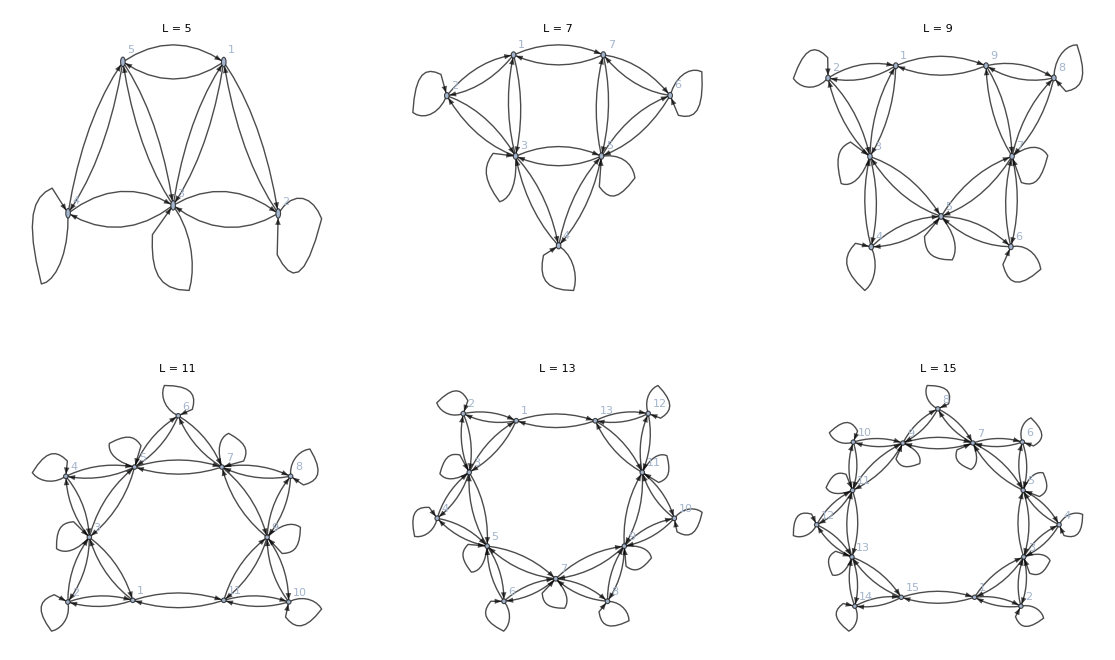

```mathematica
Print@GraphicsGrid[Partition[ParityHybridCAGraph[#]&/@Range[5,15,2],3]]
```

```mathematica
ParityHybridCAGraph[N_Integer]:=
Module[{g, edges,edge1,edgeN,evenEdges,oddEdges,fiveInDegreeVertices,threeInDegreeVertices,edgeQuantityToFiveInDegreeVertices,edgeQuantityToThreeInDegreeVertices},
edge1={N->1,2->1,3->1};
edgeN={1->N,N-1->N,N-2->N};
evenEdges=Flatten[({#->#,#-1->#,#+1->#}&/@Range[2,N-1,2])];
oddEdges=Flatten[({#->#,#-2->#,#-1->#,#+1->#,#+2->#}&/@Range[3,N-2,2])];
edges=Join[edge1,edgeN,evenEdges,oddEdges];
g=Graph[edges,EdgeStyle->Black,VertexLabels->"Name", PlotLabel->Row[{Style["L",Italic,Black, FontSize->16],Style[" = "<>ToString[N],FontSize->16]}]];
fiveInDegreeVertices=First/@Select[MapThread[List,{VertexList[g],VertexInDegree[g]}],(Last[#]==5)&];
threeInDegreeVertices=First/@Select[MapThread[List,{VertexList[g],VertexInDegree[g]}],(Last[#]==3)&];
Print[{edgeQuantityToFiveInDegreeVertices=Length@Flatten[Module[{node=#},Cases[EdgeList[g],_->node]]&/@fiveInDegreeVertices],edgeQuantityToThreeInDegreeVertices=Length@Flatten[Module[{node=#},Cases[EdgeList[g],_->node]]&/@threeInDegreeVertices]}];
HighlightGraph[g,{Style[(_->#)&/@fiveInDegreeVertices,Red]}]
];
```

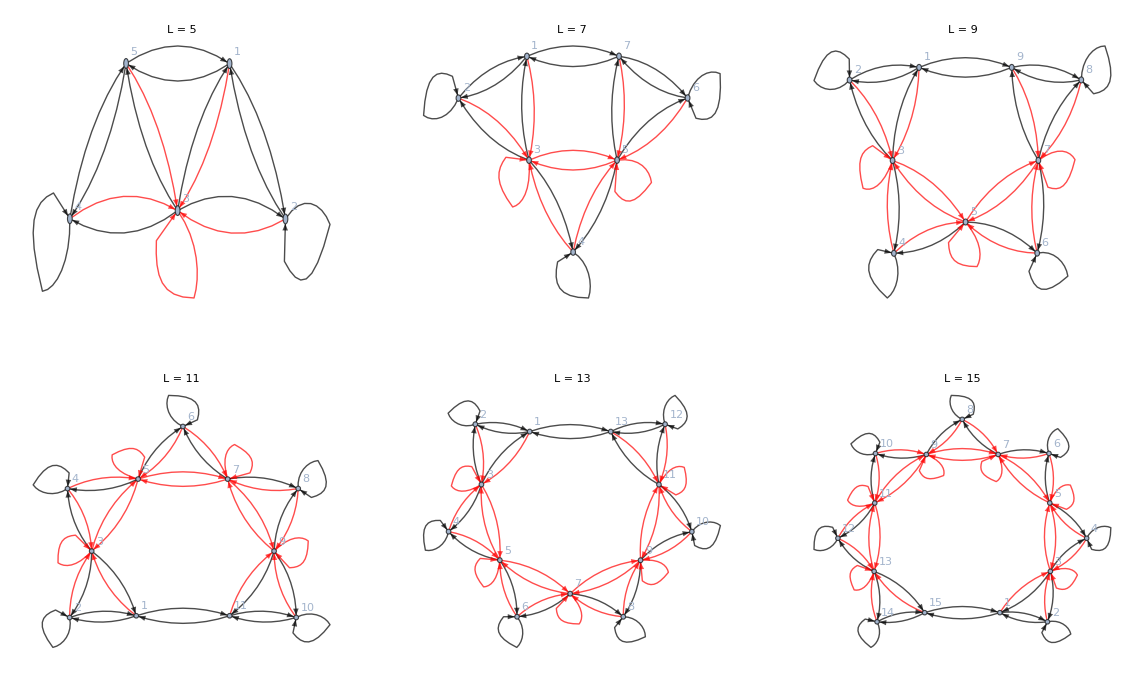

```mathematica
Print@GraphicsGrid[Partition[ParityHybridCAGraph[#]&/@Range[5,15,2],3]]
```

```mathematica
FullSimplify[5(L-3)/2+3(L+3)/2]
```

-3+4 L

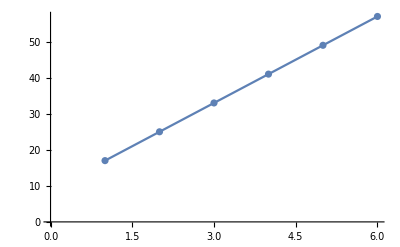

```mathematica
ListPlot[Table[4L-3,{L,5,15,2}],Joined->True,Mesh->All,PlotLegends->"Number of edges"]
```

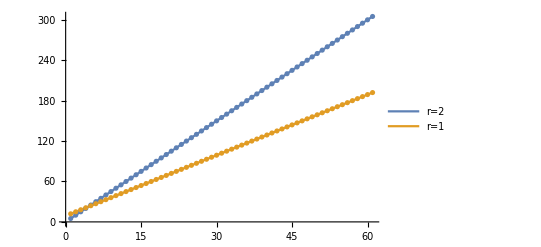

```mathematica
ListPlot[{Table[5(L-3)/2,{L,5,125,2}],Table[3(L+3)/2,{L,5,125,2}]},Joined->True,Mesh->All,PlotLegends->{"r=2","r=1"}]
```

```mathematica
FindSequenceFunction@Table[5(L-3)/2,{L,5,125,2}]/FindSequenceFunction@Table[3(L+3)/2,{L,5,125,2}]
```

(5 #1&)/(3 (3+#1)&)

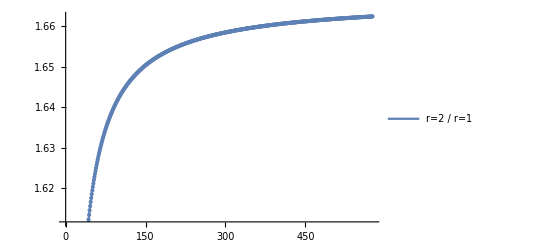

```mathematica
ListPlot[Table[(5 L)/(3 (3+L)),{L,5,1155,2}],Joined->True,Mesh->All,PlotLegends->{"r=2 / r=1"}]
```

```mathematica
5./3
```

1.66667

## Kévin 1: There seems to be an additional asynchronous update that also solves parity classification with ECA rule 150, when Mod[N, 4] = 3 (tested for N = 5, 7, 9, 11).

*for n = 5 only ({even}, {odd})
*for n = 7, ({even}, {odd}) and ({2, 6}, {1, 3, 4, 5, 7})
*for n = 9, only ({even}, {odd}) 
*for n = 11, ({even}, {odd}) and ({2, 4, 8, 10}, {1, 3, 5, 6, 7, 9, 11})

So it may be interesting to understand precisely what is the set of update schedules solving PP for a given odd n. Starting from some large n, is there only ({even}, {odd}) or does it depend on n mod 4 equal to 1 or 3?

```mathematica
Mod[#,4]&/@{5,9,13}
Mod[#,4]&/@{7,11,15}
```

{1,1,1}

{3,3,3}

### Tests

```mathematica
Module[{len=5},
Select[{EvalRuleInPP[{AsynchronousCA,{150,2,1},Tuples[{0,1},len],2^len+1,#},{}],#}&/@UDSRepsAllICs[CABooleanNetwork[1,len]],(First[#]==2^len)&]]
```

{{32.,{{1,3},{2,4,5}}}}

```mathematica
Module[{len=7},
Select[{EvalRuleInPP[{AsynchronousCA,{150,2,1},Tuples[{0,1},len],2^len+1,#},{}],#}&/@UDSRepsAllICs[CABooleanNetwork[1,len]],(First[#]==2^len)&]]
```

{{128.,{{1,4},{2,3,5,6,7}}},{128.,{{1,3,5},{2,4,6,7}}}}

```mathematica
Module[{len=9},
Select[{EvalRuleInPP[{AsynchronousCA,{150,2,1},Tuples[{0,1},len],2^len+1,#},{}],#}&/@UDSRepsAllICs[CABooleanNetwork[1,len]],(First[#]==2^len)&]]
```

{{512.,{{1,3,5,7},{2,4,6,8,9}}}}

```mathematica
EvalRuleInPP[{AsynchronousCA,{150,2,1},Tuples[{0,1},11],2^11+1,{{2,4,8,10},{1,3,5,6,7,9,11}}},{}]
```

2048.

```mathematica
Module[{len=11},
Select[{EvalRuleInPP[{AsynchronousCA,{150,2,1},Tuples[{0,1},len],2^len+1,#},{}],#}&/@UDSRepsAllICs[CABooleanNetwork[1,len]],(First[#]==2^len)&]]
```

```mathematica
EvalRuleInPP[{AsynchronousCA,{150,2,1},Tuples[{0,1},15],2^15+1,{{2,4,6,10,12,14},{1,3,5,7,8,9,11,13,15}}},{}]
```

32768.